{A→0.530224,B→-0.284303}

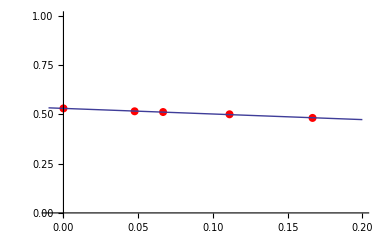

Effective bare squared mass at λ = 3.22581 is 1.10491, mean link is 0.469776

I0 = 0.245043, I1 = 0.729249

Leading order results:

g00 = 0.790463, g01 = 0.202359 , correction to the bare mass is -2.35242

Next-to-Leading order results:

g00 = 1.41032, g01 = 0.528561

0.729249 0.154791 0.245043, Res: 0.046535

```mathematica
(* Tables of data from hep-lat/9401029 *)
b020data={{1/15,0.781405},{1/21,0.781427},{1/30,0.781422}};
b031data={{1/6,0.48187},{1/9,0.50030},{1/15,0.51178},{1/21,0.51548}};
b032data={{1/9, 0.47234},{1/15,0.48072}};
(* Choosing the parameters *)
λ=1/0.31;
bdata = b031data;
(* Extrapolating the numerical results to infinite N *)
FFF=FindFit[bdata,A+B x,{A,B},x]
AppendTo[bdata,{0,A/.FFF}];
Gr1=ListPlot[bdata,PlotRange->{{-0.01,0.2},{0.0,1.0}},PlotStyle->{PointSize[0.015],RGBColor[1,0,0]}];
Gr2=Plot[(A+B x)/.FFF,{x,-0.01,0.2}];
Show[Gr1,Gr2]
(* Lowest-order corrections from SDs *)
MeanLink=(1-A)/.FFF;
m2=(λ - 4 A)/.FFF;
Print["Effective bare squared mass at λ = ",λ," is ",m2,", mean link is ",MeanLink];
I0=1/(2π)^2 NIntegrate[1/(m2 + 4 Sin[kx/2]^2+4 Sin[ky/2]^2),{kx,-π,π},{ky,-π,π}];
I1 = 1/(2π)^2 NIntegrate[(4 Sin[kx/2]^2+4 Sin[ky/2]^2)/(m2 + 4 Sin[kx/2]^2+4 Sin[ky/2]^2),{kx,-π,π},{ky,-π,π}];
Print["I0 = ",I0,", I1 = ",I1];
Print["Leading order results: "];
g00lo=λ I0; 
g01lo=λ 1/(2π)^2 NIntegrate[Cos[kx]/(m2 + 4 Sin[kx/2]^2+4 Sin[ky/2]^2),{kx,-π,π},{ky,-π,π}];
Print["g00 = ",g00lo,", g01 = ",g01lo," , correction to the bare mass is ",-λ I1];
Print["Next-to-Leading order results: "];
g00nlo=g00lo + λ^2 I1  1/(2π)^2 NIntegrate[1/((m2 + 4 Sin[kx/2]^2+4 Sin[ky/2]^2)^2),{kx,-π,π},{ky,-π,π}]; 
g01nlo=g01lo + λ^2 I1 1/(2π)^2 NIntegrate[Cos[kx]/((m2 + 4 Sin[kx/2]^2+4 Sin[ky/2]^2)^2),{kx,-π,π},{ky,-π,π}];
Print["g00 = ",g00nlo,", g01 = ",g01nlo];
(* Sign of some contribution at nnl0 *)
A0=1/(2π)^2 NIntegrate[(4 Sin[kx/2]^2+4 Sin[ky/2]^2)/(m2 + 4 Sin[kx/2]^2+4 Sin[ky/2]^2),{kx,-π,π},{ky,-π,π}];
A1=1/(2π)^2 NIntegrate[(4 Sin[kx/2]^2+4 Sin[ky/2]^2)/((m2 + 4 Sin[kx/2]^2+4 Sin[ky/2]^2)^2),{kx,-π,π},{ky,-π,π}];
S0=1/(2π)^2 NIntegrate[1/(m2 + 4 Sin[kx/2]^2+4 Sin[ky/2]^2),{kx,-π,π},{ky,-π,π}];
Print[A0," ",A1," ",S0,", Res: ",A0 A1 - m2 S0^2];
```